## Function Documentation

### This is a clickable list of functions that provide some documentation

```mathematica
?Mechanisms`*
```

```mathematica
?Mechanisms`geometry`*
```

```mathematica
?Mechanisms`rigidity`*
```

```mathematica
?Mechanisms`Origami`*
```

```mathematica
?Mechanisms`graphics`*
```

## Functions

### cells

A cell has the form
	head[ indices ]
where head is one these

```mathematica
DefaultCellData[]
```

{RigidBar,Spring,Face,ElasticTriangle,TorsionalFold,FreeJoint,PinnedJoint,AngleJoint}

You can also have a head that is an arbitrary string.

### specifying cells and their properties

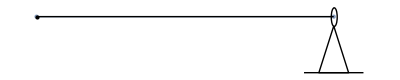

```mathematica
m=Linkage[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
```

You can include several sets of indices in each cell.

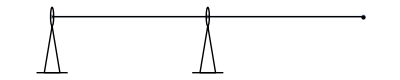

```mathematica
m=Linkage[{{0,0},{1,0},{2,0}},{RigidBar[{{1,2},{2,3}}],PinnedJoint[{1,2}]}]
```

Cell properties can also be specified. Each cell has three universal properties, “style”, “shape” and “label” which can be used to affect how they are displayed. Other properties can be accessed through defaultData[]

```mathematica
DefaultCellData[RigidBar]
```

{EquilibriumLength→Automatic,Stiffness→∞}

You can specify these in one of two ways

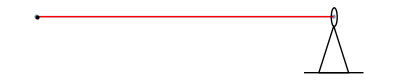

```mathematica
m=Linkage[{{0,0},{1,0}},{Property[RigidBar[{1,2}],"Style"->{Red}],PinnedJoint[2]}]
```

```mathematica
m=Linkage[{{0,0},{1,0}},{RigidBar[{1,2},{"Style"->Red}],PinnedJoint[2]}]
```

-Graphics-

Properties can be nested and can be distributed across several cells.

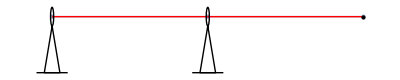

```mathematica
m=Linkage[{{0,0},{1,0},{2,0}},{RigidBar[{{1,2},{2,3}},"Style"->Red],PinnedJoint[{1,2}]}]
```

Unrecognized properties are ignored.

### mechanism types

There are two types of mechanisms with heads framework and origami. These are identical except for how they render.

All mechanisms are defined similarly to how MeshRegion[] objects are defined in Mathematica.

Linkage[ list of coordinates, list of cells]
Origami[ list of coordinates, list of cells]

They take the same options as MeshRegion with one additional option, “overlapPrecision”, which defines the numerical distance at which two vertices will be considered the same.

Frameworks basically act as is. Origami is always embedded in 3D but when the z coordinates are sufficiently close to zero, they are rendered in 2D as a fold pattern.

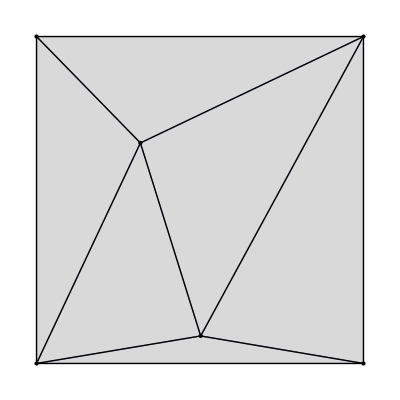

```mathematica
m=RandomOrigami[2]
```

Cells might also render differently.

-Graphics-

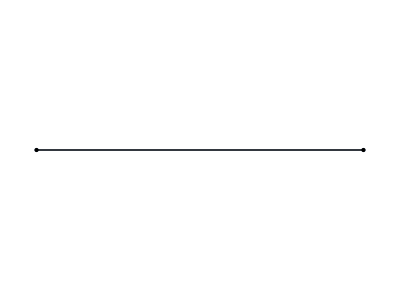

```mathematica
Linkage[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
Origami[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
```

### Extracting information from mechanisms

#### MechanismCellList[]

```mathematica
?MechanismCellList
```

Get a list of all the cells in a mechanism and the data that has been specified.

```mathematica
MechanismCellList[ f=RandomOrigami[1]]
```

{FreeJoint[{1,2,3,4,5}]→{{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}}},Face[{{1,5,4},{4,5,3},{5,1,2},{5,2,3}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}},RigidBar[{{1,2},{2,3},{2,5},{3,4},{3,5},{4,1},{5,1},{5,4}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Get the data for only a specific set of cells of a certain type.

```mathematica
MechanismCellList[ f=RandomOrigami[1], {Face, {{1,5,4},{5,3,4}}}]
```

{Face[{{1,5,4},{4,5,3}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}}}

```mathematica
MechanismCellList[ f=RandomOrigami[1],Face[{__,1,__}]]
```

{Face[{{1,5,4},{5,1,2}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}}}

Get data for any cell having data “stiffness” set to Infinity

```mathematica
MechanismCellList[ f=RandomOrigami[1],_,"Stiffness" -> Infinity]
```

{RigidBar[{{1,2},{1,5},{2,3},{3,4},{4,1},{5,2},{5,3},{5,4}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

#### ListVertices[], ListEdges[], InteriorEdges[], ListFaces[]

```mathematica
m=RandomOrigami[3];
```

```mathematica
MechanismFaces[m]
MechanismEdges[m]
```

{{1,5,4},{2,6,1},{4,5,3},{5,6,7},{5,7,3},{6,5,1},{7,2,3},{7,6,2}}

{{1,5},{5,4},{4,1},{2,6},{6,1},{1,2},{5,3},{3,4},{5,6},{6,7},{7,5},{7,3},{7,2},{2,3}}

```mathematica
InteriorEdges[m]
```

{{1,5},{5,4},{2,6},{6,1},{5,3},{5,6},{6,7},{7,5},{7,3},{7,2}}

#### MechanismConnectivity[]

```mathematica
?MechanismConnectivity
```

```mathematica
MechanismConnectivity["Methods"]
```

{{vertices,edges,faces}→{vertices,edges,faces,ordered faces,ordered edges}}

This function is used to work out what vertices, edges, and faces are connected to each other. It returns a list for each element of the left hand side of the rule and indicates all of the objects it is connected to on the right-hand side of the rule. To find all edges connected to each vertex, for example:

```mathematica
MechanismConnectivity[ m=RandomOrigami[3] , "vertices" -> "edges" ]
```

{{{1,2},{1,6},{1,7},{1,4}},{{2,6},{2,3},{2,1},{2,5}},{{3,5},{3,7},{3,4},{3,2}},{{4,7},{4,1},{4,3}},{{5,2},{5,6},{5,3},{5,7}},{{6,1},{6,2},{6,5},{6,7}},{{7,5},{7,6},{7,1},{7,3},{7,4}}}

If the object is oriented (see orientedQ[]) you can get the edges and faces in counterclockwise order.

```mathematica
MechanismConnectivity[ m , "vertices" -> "ordered edges" ]
```

{{{1,2},{1,6},{1,7}},{{2,3},{2,5},{2,6}},{{3,4},{3,7},{3,5}},{{4,1},{4,7}},{{5,3},{5,7},{5,6},{5,2}},{{6,7},{6,1},{6,2},{6,5}},{{7,3},{7,4},{7,1},{7,6},{7,5}}}

### manipulating mechanisms

#### ChangeCellData[]

```mathematica
?ChangeCellData
```

Make some random origami and extract the equilibrium lengths of all the edges.

```mathematica
MechanismCellList[ f= RandomOrigami[3], _RigidBar]
```

{RigidBar[{{1,2},{1,7},{2,3},{2,7},{3,4},{4,1},{5,3},{5,4},{6,2},{6,3},{6,5},{7,4},{7,5},{7,6}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Change all the length’s of rigidBar’s matching a particular pattern. Notice the order of the indices does not matter.

```mathematica
MechanismCellList[ 
ChangeCellData[ f,RigidBar[{1,_}],"EquilibriumLength"->1 ],
 _RigidBar]
```

{RigidBar[{{1,2},{1,7},{2,3},{2,7},{3,4},{4,1},{5,3},{5,4},{6,2},{6,3},{6,5},{7,4},{7,5},{7,6}}]→{{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Add labels to a mechanism.

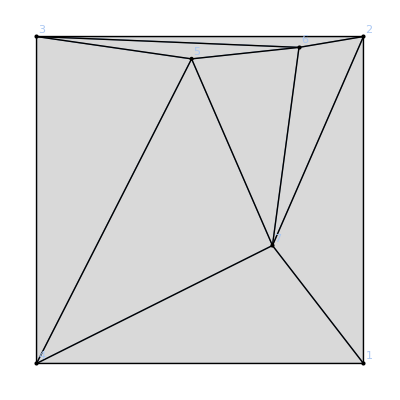

```mathematica
ChangeCellData[f,_FreeJoint,"Label"->"Index" ]
```

#### DeleteCells[]

```mathematica
?DeleteCells
```

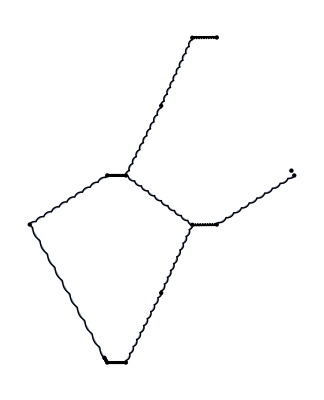

```mathematica
DeleteCells[ RandomCellNetwork[3], _[{1,_}]]
```

delete faces associated with vertex 1.

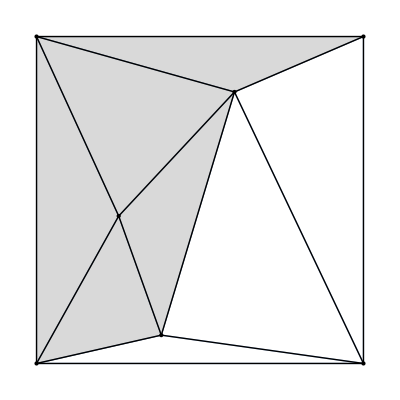

```mathematica
DeleteCells[ f=RandomOrigami[3],Face[{___,1,___}]]
```

Delete all cells associated with vertex 1. Note that the vertex itself remains.

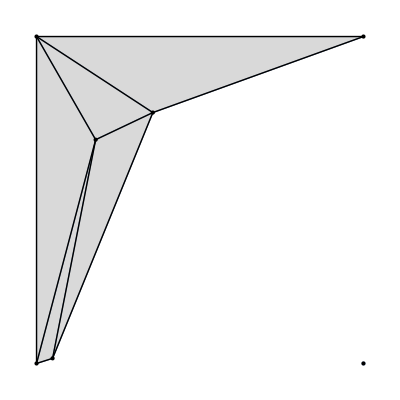

```mathematica
DeleteCells[ f=RandomOrigami[3],_[{___,1,___}]]
```

#### AddCells[]

```mathematica
?AddCells
```

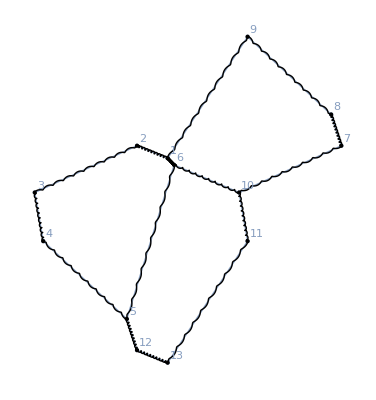

```mathematica
m=ChangeCellData[RandomCellNetwork[3],_FreeJoint,"Label"->"Index"]
```

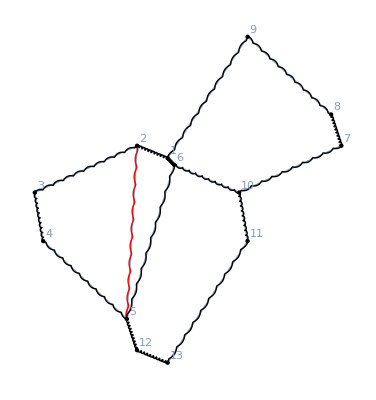

```mathematica
AddCells[ m, { Property[ Spring[{2,5}] , { "Style" -> Red } ]} ]
```

You can also overwrite existing parts of an mechanisms.

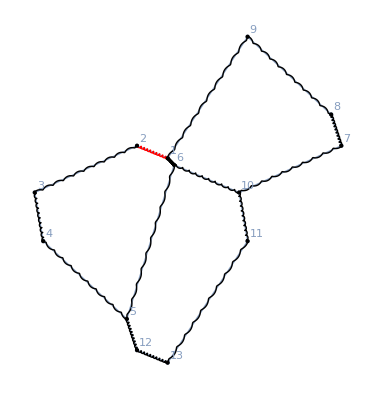

```mathematica
m2=AddCells[ m, { Property[ Spring[{2,1}] , { "Style" -> Red } ]} ]
```

```mathematica
MechanismCellList[m2,Spring[{2,1}]]
```

{Spring[{{2,1}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Strain→((#1-#2)/#2&),Shape→Automatic,Label→None,Style→{RGBColor[1, 0, 0]}}}}

#### deleting and adding vertices with AddCells[] and DeleteVertices[]

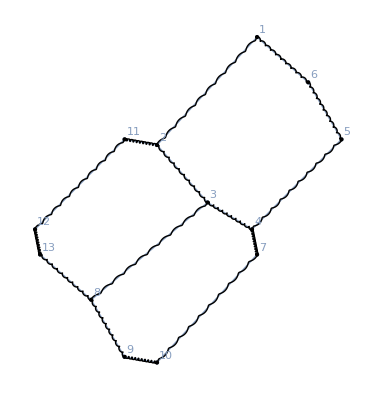

```mathematica
m=ChangeCellData[RandomCellNetwork[3],_FreeJoint,"Label"->"Index"]
```

You can add a vertex with addCell using the notation joint[ name -> position ] where label is a name to use to refer to the point and position are the coordinates of the new vertex. You then refer to the new vertex using its name.

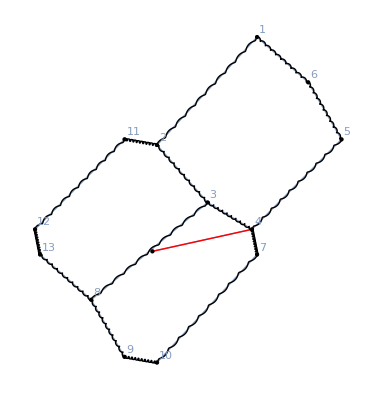

```mathematica
AddCells[ m, {FreeJoint[ "a"->{0,-1/4}], RigidBar[{"a",4},"Style"->Red]}]
```

deleteVertices[] deletes a vertex and everything connected to it.

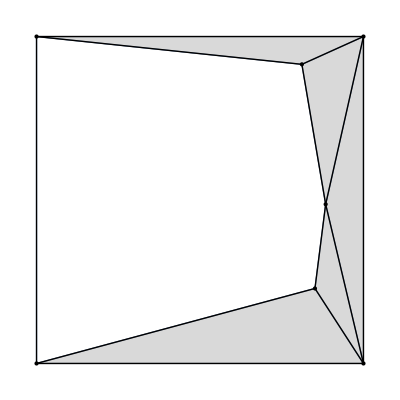

```mathematica
DeleteVertices[ m=RandomOrigami[4], {5}]
```

#### SelectCells[]

```mathematica
?SelectCells
```

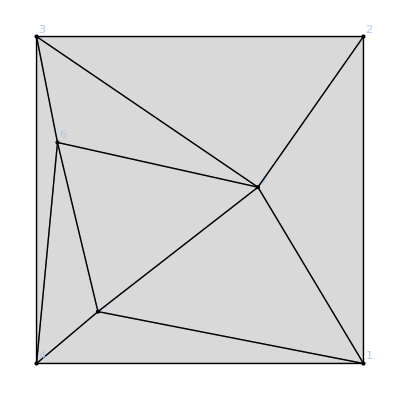

```mathematica
f=ChangeCellData[_FreeJoint,"Label"->"Index"]@RandomOrigami[3]
```

Select all the cells that are joined to vertex 1.

MeshRegion::pnset: Some or all of the properties specified in the Properties option could not be set.

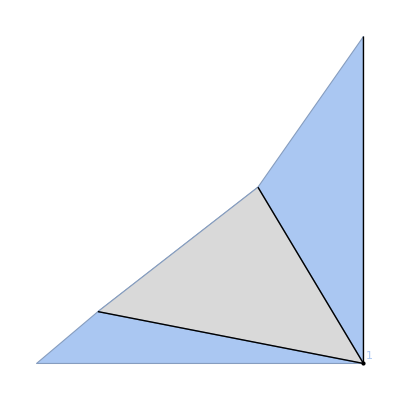

```mathematica
f2=ChangeCellData[_FreeJoint,"Label"->"Index"]@SelectCells[f,_[1]|_[{___,1,___}]]
```

```mathematica
MechanismCellList[f]
```

{FreeJoint[{1,2,3,4,5,6,7}]→{{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}}},Face[{{1,5,4},{2,7,1},{5,6,4},{6,3,4},{7,2,3},{7,3,6},{7,5,1},{7,6,5}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}},RigidBar[{{1,2},{1,5},{2,3},{3,4},{3,6},{3,7},{4,1},{5,4},{5,7},{6,4},{6,5},{6,7},{7,1},{7,2}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

```mathematica
MechanismCellList[f2]
```

{FreeJoint[{1}]→{{Shape→Automatic,Label→Index,Style→{}}},Face[{{1,5,4},{2,7,1},{7,5,1}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}},RigidBar[{{1,2},{1,5},{4,1},{7,1}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Keep all the rigid bars connected to vertex 1 but all the faces in the structure.

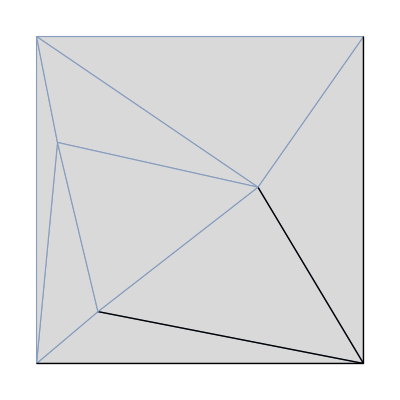

```mathematica
f2=SelectCells[f,Face[_]| RigidBar[{___,1,___}]]
```

#### DisplaceVertices[]

```mathematica
?DisplaceVertices
```

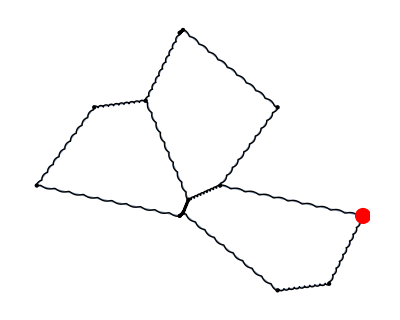
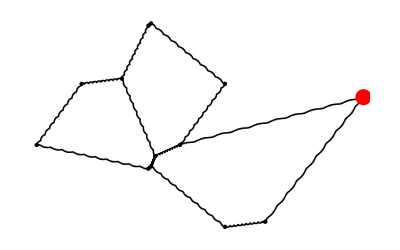

```mathematica
{
f=ChangeCellData[FreeJoint[1],"Style"->{Red,PointSize[0.029]}]@RandomCellNetwork[3],
DisplaceVertices[ f, {1->{0.5,0.5}} ]
}
```

```mathematica
DisplaceVertices[ RandomOrigami[2], RandomReal[ {-0.1,0.1}, {6,3}]]
```

-Graphics3D-

#### SubdivideCell[]

```mathematica
?SubdivideCells
```

Create a vertex on an edge and displace it.

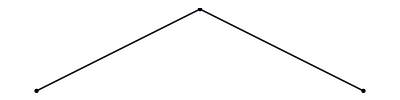

```mathematica
DisplaceVertices[{"a"->{0,1/4}}]@SubdivideCells[Linkage[ {{0,0},{1,0}}, {RigidBar[{1,2}]}],{{1,2}},"a"]
```

#### Henneberg[]

Henneberg operations acting on a 2D linkage preserve the number of degrees of freedom (generically).

```mathematica
?Henneberg
```

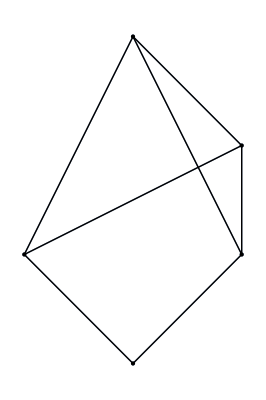

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}]
```

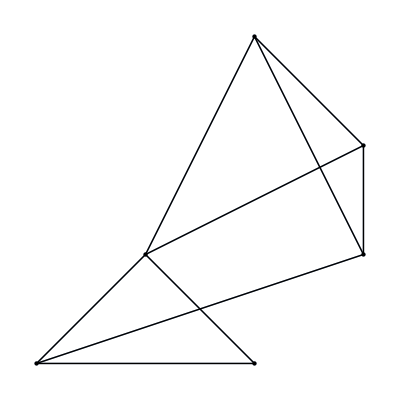

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

#### JoinMechanism[]

```mathematica
?JoinMechanism
```

```mathematica
JoinMechanism[ RandomOrigami[2], #+{0,0,1}& /@ RandomOrigami[3] ]
```

-Graphics3D-

Two vertices that are sufficiently close together will be merged. Use “overlapPrecision” to specify how close to operate this.

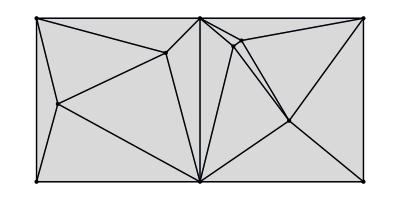

```mathematica
JoinMechanism[ RandomOrigami[2], #+{Sqrt[2],0,0}& /@ RandomOrigami[3] ]
```

## Examples

## basic examples

### building new frameworks

```mathematica
f=Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}]
```

-Graphics-

There are two formats:

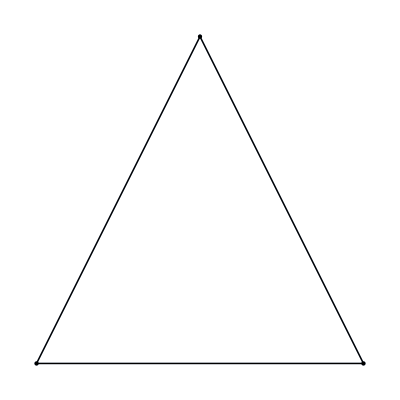

```mathematica
AddCells[ f,  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ]
```

```mathematica
AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ f
```

-Graphics-

This version allows constructions by sequential composition

#### Henneberg operations

```mathematica
?Henneberg
```

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ f
```

-Graphics-

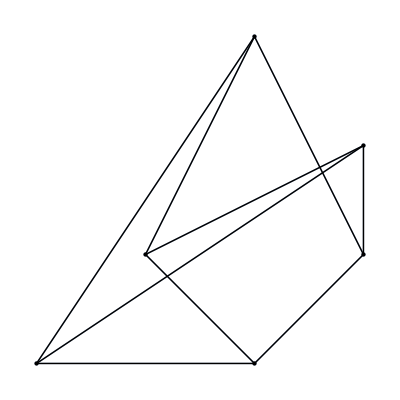

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

### special mechanism examples

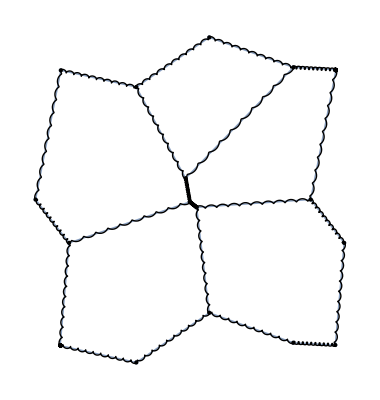

```mathematica
RandomCellNetwork[5]
```

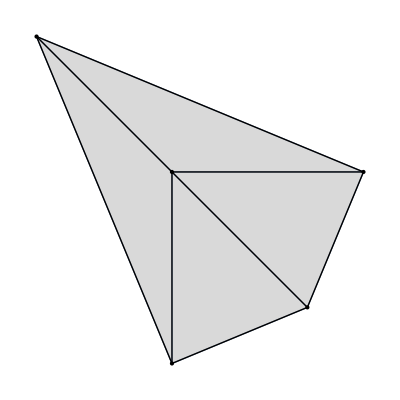

```mathematica
m=SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

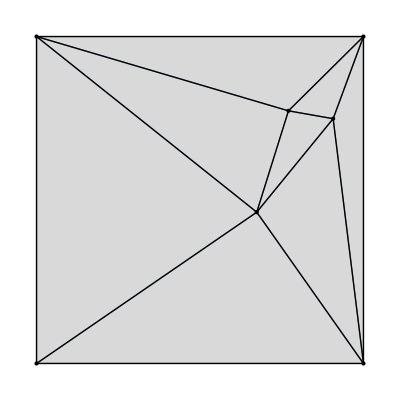

```mathematica
RandomOrigami[3]
```

## mechanism examples

### Watt mechanism

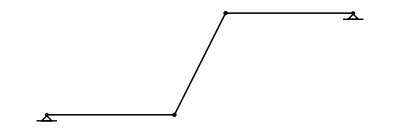

```mathematica
wattMechanism = Linkage[ {{0,0},{1+1/4,0},{2-1/4,1},{3,1}}, {RigidBar[{{1,2},{2,3},{3,4}}], PinnedJoint[1],PinnedJoint[4]} ]
```

```mathematica
im=MechanismInfinitesimalMotions[ wattMechanism ,OutputVariables -> v ]
```

{{{0,0},{0,v[1]/(√2)},{0,v[1]/(√2)},{0,0}},{}}

```mathematica
direction = D[im[[1]],v[1]]
```

{{0,0},{0,1/(√2)},{0,1/(√2)},{0,0}}

```mathematica
MechanismZeroModes[wattMechanism]
```

{{{0,0},{0,1},{0,1},{0,0}}}

```mathematica
trajectory = MechanismIsometricTrajectory[ wattMechanism, direction, 100 ];
```

```mathematica
(*The center of the middle bar position *)
centerTrace = Mean /@ trajectory[[All, {2,3}]] ;
centerTrail = Table[ centerTrace[[1;;i]], {i,1,Length[centerTrace]}];
```

```mathematica
ListAnimate @ 
MapThread[
Show[#1,Graphics[{Blue,Point[#2]}]]&,
{
PlotMechanism[ wattMechanism, trajectory ],
centerTrail
}
]
```

### origami bird’s foot vertex

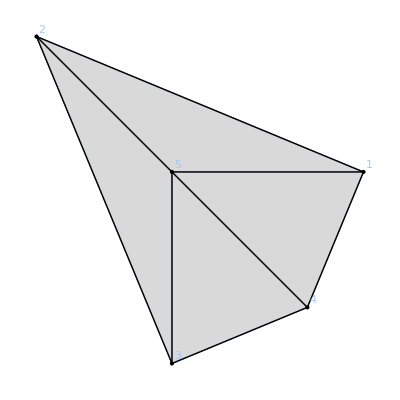

```mathematica
ChangeCellData[_FreeJoint , "Label"->"Index"]@(o=AddCells[ { Property[ TorsionalFold[{1,5}] ,  "Angle"-> Pi/2 ] } ] @SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}])
```

```mathematica
{en, pos } = MinimizeMechanismEnergy[o]
```

{1.31796×10^-20,{{0.933586,-0.100663,-0.255571},{-0.610404,0.579642,0.497751},{0.118282,-0.916883,-0.304523},{0.606038,-0.617808,0.203841},{-0.0475022,0.0557107,-0.141497}}}

```mathematica
PlotMechanism[o,pos]
```

-Graphics3D-

```mathematica
{ linear, quadratic} = FullSimplify[
MechanismInfinitesimalMotions[o = SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}], Constraints->{VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]} ,
OutputVariables -> v]
]
```

{{{0,0,v[2]},{0,0,0},{0,0,0},{0,0,v[1]},{0,0,0}},{-(v[1] (v[1]-√2 v[2]))/(2 √3)}}

```mathematica
dir = D[ linear /. Solve[quadratic==0,{v[1],v[2]}] /. {v[1]->v,v[2]->v},v]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{0,0,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,1/(√2)},{0,0,0},{0,0,0},{0,0,1},{0,0,0}}}

```mathematica
trajectory1 = Join[
Reverse @MechanismIsometricTrajectory[ o, -dir[[1]],180,Constraints -> {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]},StepSize -> 0.02][[All,{4,1},3]]

,
 MechanismIsometricTrajectory[ o, dir[[1]],180,Constraints ->  {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]}, StepSize-> 0.02][[All,{4,1},3]]
];

trajectory2 = Join[
Reverse @MechanismIsometricTrajectory[ o, -dir[[2]],180,Constraints ->  {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]}, StepSize -> 0.02][[All,{4,1},3]]

,
 MechanismIsometricTrajectory[ o, dir[[2]],180,Constraints -> {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]}, StepSize -> 0.02][[All,{4,1},3]]
];
```

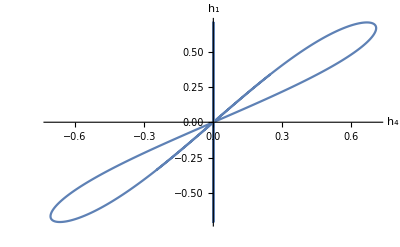

```mathematica
Show[
ListPlot[trajectory1,Joined->True],
ListPlot[trajectory2, Joined->True],

PlotRange->All,AxesLabel->{Subscript["h",4],Subscript["h",1]}
]
```

## periodic mechanisms

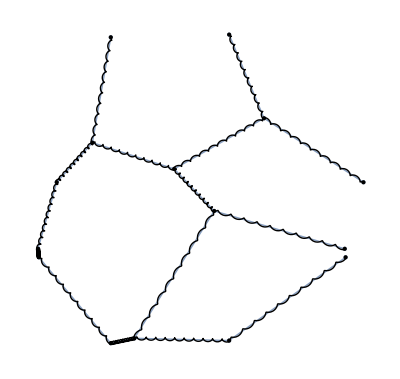

```mathematica
m=MechanismUnitCell[ m0=RandomCellNetwork[5], {{1,0},{0,1}}]
```

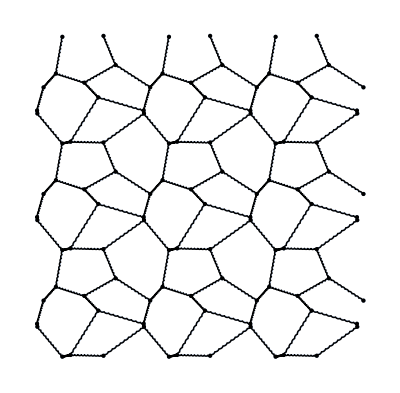

```mathematica
TesselateMechanism[ m , {{1,0},{0,1}},{3,3}]
```

```mathematica
pi=PeriodicIdentification[ m,  {{1,0},{0,1}} ]
```

PeriodicIdentificationData[{{1,0},{0,1}}]

```mathematica
MechanismConstraintMatrix[m, EliminationRules -> pi["DisplacementRules"] ]
```

SparseArray[…]

```mathematica
m2=ChangeCellData[m, _Spring ,  "EquilibriumLength" -> 0.05]
```

-Graphics-

```mathematica
{en, pos} = MinimizeMechanismEnergy[m2, Constraints -> pi["Constraints"],MaxIterations->10^4]
```

{293.908,{{-0.044191,-0.35729},{0.0563526,-0.107912},{-0.151038,0.0178628},{-0.358429,-0.107912},{-0.257885,-0.35729},{0.0563526,-0.606669},{-0.358429,-0.606669},{-0.151038,-0.732443},{-0.151038,0.267557},{-0.651038,0.270869},{-0.651038,0.0145508},{-0.943647,-0.107912},{-1.04419,-0.35729},{-0.943647,-0.606669},{-0.651038,-0.729131}}}

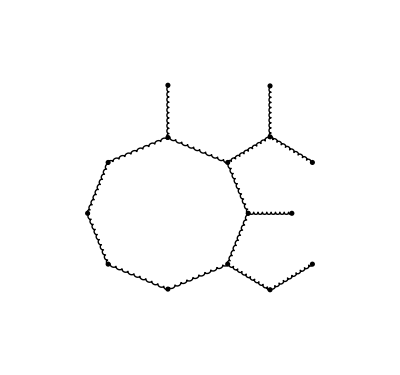

```mathematica
PlotMechanism[ m, pos ]
```